# PPPC Machine Runner Addendum

Flip Tanedo
23 Feb 2015

Needs PPPCMachine.

## Define Functions

Reference:

```mathematica
p2gam[primary_,pE_,photonE_]:=If[photonE<pE,
10^(dlNdlxIEW[primary->"γ"][pE,Log[10,photonE/pE]])/(Log[10.] photonE),
0 (* if photon energy is larger than injection energy *)
] (* usage: primary is of the form "τ", WITH the quotation marks *)
```

```mathematica
tenergy[mx_]:=Module[{mt,mc},
mt=174.;
mc=1.2;
(4 mx^2+mt^2-mc^2)/(4mx)]

cenergy[mx_]:=Module[{mt,mc},
mt=174.;
mc=1.2;
(4 mx^2+mc^2-mt^2)/(4mx)]
```

```mathematica
p2tc[mx_,photonE_]:=If[
photonE<180. (*~mt + mc + wiggle room *)
&&
2mx>180.
&&
tenergy[mx]≥180
,1/2 p2gam["t",tenergy[mx],photonE]+1/2 p2gam["c",cenergy[mx],photonE],0]
```

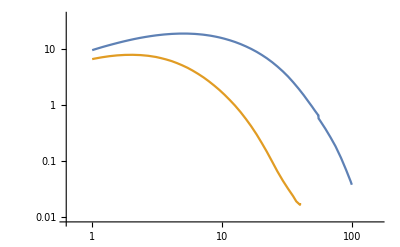

```mathematica
LogLogPlot[{x^2 p2tc[119,x],x^2 p2gam["b",40,x]} ,{x,1,100}]
```

## Caveats

Note that PPPC wants the top to have a minimum energy of 180 GeV, this enforces mx > 120.

```mathematica
tenergy[100]
```

175.686

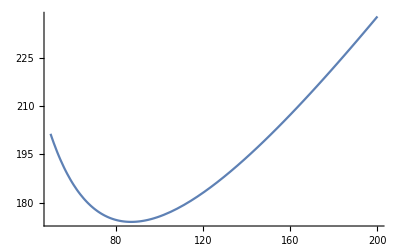

```mathematica
Plot[tenergy[x],{x,50,200}]
```

```mathematica
p2gam["t",180,1]
```

13.7986

```mathematica
p2gam["t",179,1]
```

InterpolatingFunction::dmval: Input value {179, -Log[179]/Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

13.8138

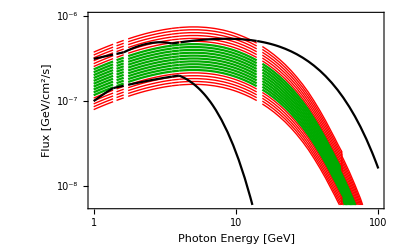

```mathematica
SuperPlot[p2tc[119,#]&,
RangeOfNorms[p2tc[119,#]&,MinEnv,MaxEnv,2,2,20]
,MinEnv,MaxEnv,1.5,20,1,100]
```

## PPPC Runner Style

```mathematica
Interpoltc[mχ_ (*>120*),minEγ_ (*.1*),maxEγ_ (*140*),nγbins_ (* 100 *),filename_]:=Module[
{mchi=mχ,minEgam=minEγ,maxEgam=maxEγ,Ngam=nγbins,path=filename,samplepoints},

samplepoints=10^#&/@Range[Log[10,minE],Log[10,maxE],(Log[10,maxE]-Log[10,minE])/Ngam];

SaveIt[path<>"_"<>ToString[mchi],{
{mchi,minEgam,maxEgam,Ngam,path},
Interpolation[{#,p2tc[mchi,#]}&/@ samplepoints]
}]
]
```

### Sanity Check

```mathematica
Interpoltc[125, .1, 140, 100,"/Users/fliptanedo/Documents/Temp/tctest"]
```

/Users/fliptanedo/Documents/Temp/tctest_125.dat

```mathematica
testread=ReadIt["/Users/fliptanedo/Documents/Temp/tctest_125"];
```

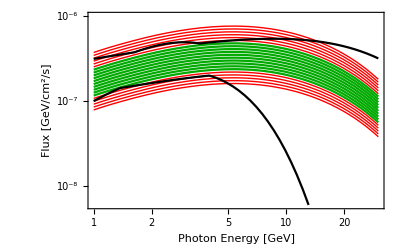

```mathematica
SuperPlot[testread[[2]],
RangeOfNorms[testread[[2]],MinEnv,MaxEnv,2,2,20]
,MinEnv,MaxEnv,1.5,20,1,30]
```

Note: there seems to be an error if I go to up to Eγ = 100. Seems to be because the function ends. But I don’t really understand why.

InterpolatingFunction::dmval: Input value {10\ 10^3/5} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {10\ 10^7/10} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

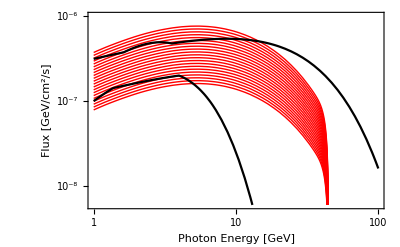

```mathematica
SuperPlot[testread[[2]],
RangeOfNorms[testread[[2]],MinEnv,MaxEnv,2,2,20]
,MinEnv,MaxEnv,1.5,20,1,100]
```

### Run, run reindeer

```mathematica
dirtc="/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc"
Interpoltc[#, .1, 140, 100,dirtc]&/@Range[120,200]
```

/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc

{/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_120.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_121.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_122.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_123.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_124.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_125.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_126.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_127.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_128.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_129.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_130.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_131.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_132.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_133.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_134.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_135.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_136.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_137.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_138.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_139.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_140.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_141.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_142.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_143.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_144.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_145.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_146.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_147.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_148.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_149.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_150.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_151.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_152.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_153.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_154.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_155.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_156.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_157.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_158.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_159.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_160.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_161.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_162.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_163.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_164.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_165.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_166.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_167.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_168.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_169.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_170.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_171.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_172.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_173.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_174.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_175.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_176.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_177.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_178.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_179.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_180.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_181.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_182.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_183.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_184.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_185.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_186.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_187.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_188.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_189.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_190.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_191.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_192.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_193.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_194.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_195.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_196.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_197.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_198.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_199.dat,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_200.dat}

## PPPC Reader Style

### Some Filenames

```mathematica
tcfilename[path_,mass_]:=path<>"_"<>ToString[mass]<>".dat"
```

```mathematica
FileExistsQ[tcfilename[dirtc,120]]
```

True

```mathematica
gettcfunc[path_,mass_]:=ReadIt[tcfilename[path,mass]][[2]]
```

### Full Tag

```mathematica
FullTagtc[path_,mass_,
MinEnv_,MaxEnv_,A_,testpoint_,numSlices_,numSamples_,minE_,maxE_]:=
Module[{func,norms},
func=gettcfunc[path,mass];
norms=GetGoodNorms[func,MinEnv,MaxEnv,A,testpoint,numSlices,numSamples,minE,maxE];

{"contact","tc",mass,tcfilename[path,mass],{Min[norms],Max[norms]},GetMinA[func,MinEnv,MaxEnv,testpoint,numSlices,numSamples,minE,maxE]
}

]
```

### Test

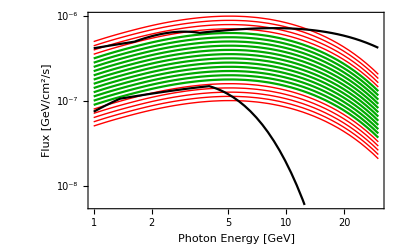

```mathematica
SuperPlot[
gettcfunc[dirtc,120],
RangeOfNorms[
gettcfunc[dirtc,120],
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
20],(* Number of divisions *)
MinEnv,MaxEnv,
2, (* Envelope Scaling *)
20, (* Number of energies to check *)
1, (* min E *)
30] (* max E *)
```

```mathematica
FullTagtc[dirtc,120,
MinEnv,MaxEnv,2,2,30,30,1,30]
```

{contact,tc,120,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_120.dat,{9.05611×10^-9,3.31203×10^-8},1.02}

### Run, Run Reindeer

```mathematica
tcdata=FullTagtc[dirtc,#,MinEnv,MaxEnv,2,2,30,30,.1,140]&/@Range[120,200];
```

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.127312} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.162085} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

$Aborted

```mathematica
SaveIt[dirtc<>"_fulltags.dat",tcdata];
```

```mathematica
tcdata[[3]]
```

{contact,tc,122,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_122.dat,{8.9781×10^-9,3.2835×10^-8},1.02}

```mathematica
Length[tcdata]
```

81

```mathematica
tcdata[[80]]
```

{contact,tc,199,/Users/fliptanedo/Documents/Work/PPPCMachineRunner/tc/tc_199.dat,{7.74821×10^-9,2.18637×10^-8},1.15}

## PPPC Reader Redo

### Full Tag

```mathematica
FullTagtc[mass_,
MinEnv_,MaxEnv_,A_,testpoint_,numSlices_,numSamples_,minE_,maxE_]:=
Module[{func,norms},
func=p2tc[mass,#]&;
norms=GetGoodNorms[func,MinEnv,MaxEnv,A,testpoint,numSlices,numSamples,minE,maxE];

{"contact","tc",mass,"nofile",{Min[norms],Max[norms]},GetMinA[func,MinEnv,MaxEnv,testpoint,numSlices,numSamples,minE,maxE]
}
]
```

```mathematica
tcdataredo=FullTagtc[#,MinEnv,MaxEnv,2,4,30,30,.1,140]&/@Range[120,121];
```

```mathematica
%
```

{{contact,tc,120,nofile,{9.10904×10^-9,3.27743×10^-8},1.02},{contact,tc,121,nofile,{9.04695×10^-9,3.25509×10^-8},1.02}}

```mathematica
tcdataredo=FullTagtc[#,MinEnv,MaxEnv,2,4,30,30,.1,140]&/@Range[120,220];
```

```mathematica
SaveIt[dirtc<>"_fulltags.dat",tcdataredo];
```

## Plotter

### Minimum A

```mathematica
minAtc={#[[3]],#[[6]]}&/@tcdataredo;
```

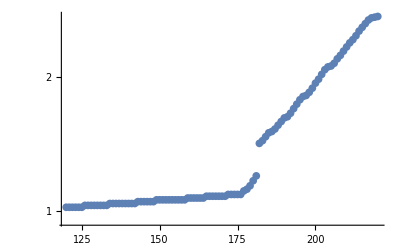

```mathematica
ListLogPlot[minAtc]
```

#### Discussion

Discussion: there’s a jump at 180. You can see why here:

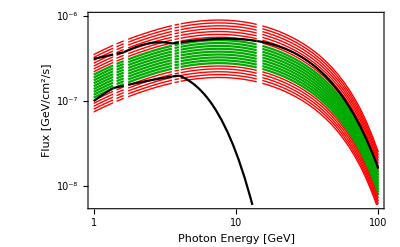

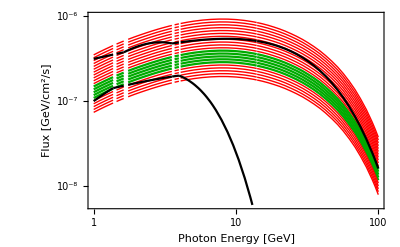

```mathematica
SuperPlot[p2tc[175,#]&,
RangeOfNorms[p2tc[175,#]&,MinEnv,MaxEnv,2,2,20]
,MinEnv,MaxEnv,1.5,20,1,100]

SuperPlot[p2tc[185,#]&,
RangeOfNorms[p2tc[185,#]&,MinEnv,MaxEnv,2,2,20]
,MinEnv,MaxEnv,1.5,20,1,100]
```

The 175 GeV plot is really brushing into the upper limit around Egam = 100. In fact, maybe some of these lines don’t survive if you extend the bounds past 100. For the 185 GeV plot, you start hitting the steep drop in the upper bound.

#### Prettify

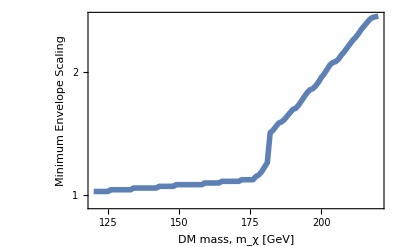

```mathematica
ListLogPlot[minAtc,
BaseStyle->{FontFamily->"Helvetica",FontSize->13},
Frame->True,
GridLines->Automatic,
Joined->True,
PlotStyle->Thickness[0.01],
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"DM mass, m_χ [GeV]","Minimum Envelope Scaling"},
(*PlotLabel->"Minimum Envelope Scaling To Fit",*)
Epilog->{
Text[Rotate[Style["χχ̄→tc",15,Darker[Black]],0Degree],ImageScaled@{.22,.92}]
}
]
```

### Range

Modify ARange to havea dummy parameter so that the other functions work.

```mathematica
ARangeTc[datum_]:=Join[{datum[[3]],0 (*dummy*)},datum[[5]]]
```

```mathematica
ConvertToFactorFromThermal/@ConvertToThermalUnits/@ARangeTc/@tcdataredo[[1;;5]]
```

{{120,0,1.38733},{121,0,1.40093},{122,0,1.41491},{123,0,1.42918},{124,0,1.44351}}

```mathematica
factorfromthermaltc=ConvertToFactorFromThermal/@ConvertToThermalUnits/@ProcessARange/@ ARangeTc/@tcdataredo;
```

```mathematica
interpoltc=Interpolation[ConvertToFactorFromThermal/@ConvertToThermalUnits2/@ProcessARange2/@ARangeTc/@tcdataredo]//Quiet;
```

```mathematica
ARangeTc[tcdataredo[[1]]]
```

{120,0,9.10904×10^-9,3.27743×10^-8}

### Range Plot

```mathematica
ARangeTcData=ProcessARange/@ARangeTc/@tcdataredo;
```

```mathematica
tcdataredo[[100;;]]
```

{{contact,tc,219,nofile,{∞,-∞},2.73},{contact,tc,220,nofile,{∞,-∞},2.74}}

#### Pretty Plot

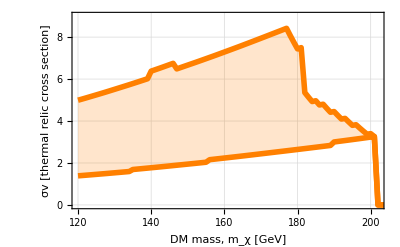

```mathematica
ListLinePlot[{{#[[1]],#[[3]]}&/@ConvertToThermalUnits/@ARangeTcData,
{#[[1]],#[[4]]}&/@ConvertToThermalUnits/@ARangeTcData},Filling->{1->{2}},
BaseStyle->{FontFamily->"Helvetica",FontSize->13},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"DM mass, m_χ [GeV]","σv [thermal relic cross section]"},
(*PlotLabel->"σv [units of thermal relic cross section]",*)
FrameStyle->Thickness[.003],
PlotRange->{{120,202},{0,9}},
(*PlotStyle->Thickness[0.01],*)
PlotStyle->{{Thickness[0.01],Orange},{Thickness[0.01],Orange}},
PlotRangeClipping->True,
Epilog->{
Text[Rotate[Style["χχ̄→tc, a=2",15,Darker[Black]],0Degree],ImageScaled@{.26,.92}]
}
]
```